### Graphene

#### TB

```mathematica
<<TopoTB`
```

```mathematica
?Wannier90hr
```

```mathematica
SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
(*Import wannier90_hr.dat file*)
wannier90hr=Import["wannier90_hr.dat","Table"];
(*Import POSCAR files, or write directly to a, b, and c without importing them*)
poscar=Import["POSCAR","Table"];
(*Import WFcenter*)
wfcentre=Import["WFcentre.txt","Table"];
(*Fermi level*)
efermi=-1.7611;
a=poscar[[3]];b=poscar[[4]];c=poscar[[5]];
lat={a,b,c};
```

```mathematica
dsLattice=Wannier90hr[wannier90hr,lat,{kx,ky,kz}]
```

Dataset[<>]

```mathematica
dsAtom=Wannier90hr[wannier90hr,lat,{kx,ky,kz},2,wfcentre]
```

Dataset[<>]

```mathematica
HLattice=Normal[dsLattice[7]];
HLattice//TraditionalForm
HLattice/.{kx->1,ky->1,kz->1}//TraditionalForm
```

(-1.27709+0.2398 ⅇ^((0.-2.46882 ⅈ) kx)+0.2398 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000052 ⅇ^((0.-25.6567 ⅈ) ky)+0.000052 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.000061 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.239801 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.239801 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000019 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.000061 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000061 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)) | -2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000142 ⅇ^((0.-9.87527 ⅈ) kx)-0.000143 ⅇ^((0.+9.87527 ⅈ) kx)+0.000273 ⅇ^((0.-12.3441 ⅈ) kx)+0.000274 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-9.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000079 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))-0.000039 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000113 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000046 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+1.×10^-6 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.00005 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))+2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))+0.000039 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))+0.000039 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.013694 ⅇ^((0.-4.27611 ⅈ) ky)-0.215067 ⅇ^((0.+4.27611 ⅈ) ky)+0.00057 ⅇ^((0.-8.55223 ⅈ) ky)-0.001909 ⅇ^((0.+8.55223 ⅈ) ky)-0.000312 ⅇ^((0.-12.8283 ⅈ) ky)-0.000236 ⅇ^((0.+12.8283 ⅈ) ky)+4.×10^-6 ⅇ^((0.-17.1045 ⅈ) ky)-0.000036 ⅇ^((0.+17.1045 ⅈ) ky)+0.000066 ⅇ^((0.-21.3806 ⅈ) ky)+0.000021 ⅇ^((0.+21.3806 ⅈ) ky)-0.000018 ⅇ^((0.-25.6567 ⅈ) ky)-0.000013 ⅇ^((0.+25.6567 ⅈ) ky)-0.000015 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000027 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000015 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))+0.000077 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000689 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000689 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000016 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-2.82749 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-2.82749 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.009282 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000081 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))+0.0000225 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))-0.000038 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000031 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000211 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000211 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.004839 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.004839 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))+7.×10^-6 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))-0.013694 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))-0.013694 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.00011 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.00011 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))+0.00057 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))+0.00057 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000167 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000027 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.011301 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.011301 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.0000395 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))-0.000039 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))-0.000039 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000057 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))-0.000312 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000689 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000371 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000027 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000027 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-9.×10^-6 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+4.×10^-6 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+0.000057 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))+0.000077 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000143 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000143 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000343 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+0.000066 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-5.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))-0.00002 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))+0.000273 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))+0.000274 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))-0.000081 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000031 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000031 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000039 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000039 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000015 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))-0.000133 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000039 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))-0.000072 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))-0.000072 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000016 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000038 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))+0.000027 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00005 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))+2.×10^-6 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000082 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000046 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.000045 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000036 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000036 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-0.000026 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-0.000026 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-6.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))+0.000015 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))+0.000015 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))
-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000143 ⅇ^((0.-9.87527 ⅈ) kx)-0.000142 ⅇ^((0.+9.87527 ⅈ) kx)+0.000274 ⅇ^((0.-12.3441 ⅈ) kx)+0.000273 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-6.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000043 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+8.×10^-6 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000038 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000016 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))+0.000274 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))+0.000273 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))+0.000182 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000081 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000081 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000016 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000015 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.215067 ⅇ^((0.-4.27611 ⅈ) ky)-0.013694 ⅇ^((0.+4.27611 ⅈ) ky)-0.001909 ⅇ^((0.-8.55223 ⅈ) ky)+0.00057 ⅇ^((0.+8.55223 ⅈ) ky)-0.000236 ⅇ^((0.-12.8283 ⅈ) ky)-0.000312 ⅇ^((0.+12.8283 ⅈ) ky)-0.000036 ⅇ^((0.-17.1045 ⅈ) ky)+4.×10^-6 ⅇ^((0.+17.1045 ⅈ) ky)+0.000021 ⅇ^((0.-21.3806 ⅈ) ky)+0.000066 ⅇ^((0.+21.3806 ⅈ) ky)-0.000013 ⅇ^((0.-25.6567 ⅈ) ky)-0.000018 ⅇ^((0.+25.6567 ⅈ) ky)-0.000036 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000046 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))-0.00005 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000031 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))-0.000343 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-0.004839 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-0.004839 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))-0.001909 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))-0.001909 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))+0.000039 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))+0.000039 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000235 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000043 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+8.×10^-6 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000236 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000236 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))+0.009282 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))+0.009282 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.000072 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.000371 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-6.×10^-6 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.000026 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000031 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000031 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000036 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))-0.000072 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.000142 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.000689 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.002413 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.000015 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000015 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000045 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+2.×10^-6 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))+0.000273 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000077 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))-0.000211 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000039 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000013 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000013 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+8.×10^-6 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000133 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))+0.000027 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))+0.000027 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+1.×10^-6 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-6.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000043 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000039 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000015 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000167 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000167 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000047 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000047 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000082 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000027 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000182 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.000057 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.000057 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000113 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000015 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000038 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00011 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.00002 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.00002 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))-5.×10^-6 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))-0.000039 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))+0.000031 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-9.×10^-6 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000018 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000018 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)) | -1.27709+0.239801 ⅇ^((0.-2.46882 ⅈ) kx)+0.239801 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000051 ⅇ^((0.-25.6567 ⅈ) ky)+0.000051 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.00006 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.2398 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.2398 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.00006 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.00006 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)))

(-1.79135+0. ⅈ | -1.44004-1.40063 ⅈ
-1.44004+1.40063 ⅈ | -1.79135+0. ⅈ)

```mathematica
HAtom=Normal[dsAtom[7]];
HAtom//TraditionalForm
HAtom/.{kx->1,ky->1,kz->1}//TraditionalForm
```

((1.+0. ⅈ) (-1.27709+0.2398 ⅇ^((0.-2.46882 ⅈ) kx)+0.2398 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000052 ⅇ^((0.-25.6567 ⅈ) ky)+0.000052 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.000061 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.239801 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.239801 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000019 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.000061 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000061 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))) | ⅇ^(ⅈ (0.-1.42537 ky)) (-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000142 ⅇ^((0.-9.87527 ⅈ) kx)-0.000143 ⅇ^((0.+9.87527 ⅈ) kx)+0.000273 ⅇ^((0.-12.3441 ⅈ) kx)+0.000274 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-9.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000079 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))-0.000039 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000113 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000046 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+1.×10^-6 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.00005 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))+2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))+0.000039 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))+0.000039 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.013694 ⅇ^((0.-4.27611 ⅈ) ky)-0.215067 ⅇ^((0.+4.27611 ⅈ) ky)+0.00057 ⅇ^((0.-8.55223 ⅈ) ky)-0.001909 ⅇ^((0.+8.55223 ⅈ) ky)-0.000312 ⅇ^((0.-12.8283 ⅈ) ky)-0.000236 ⅇ^((0.+12.8283 ⅈ) ky)+4.×10^-6 ⅇ^((0.-17.1045 ⅈ) ky)-0.000036 ⅇ^((0.+17.1045 ⅈ) ky)+0.000066 ⅇ^((0.-21.3806 ⅈ) ky)+0.000021 ⅇ^((0.+21.3806 ⅈ) ky)-0.000018 ⅇ^((0.-25.6567 ⅈ) ky)-0.000013 ⅇ^((0.+25.6567 ⅈ) ky)-0.000015 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000027 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000015 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))+0.000077 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000689 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000689 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000016 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-2.82749 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-2.82749 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.009282 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000081 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))+0.0000225 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))-0.000038 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000031 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000211 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000211 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.004839 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.004839 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))+7.×10^-6 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))-0.013694 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))-0.013694 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.00011 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.00011 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))+0.00057 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))+0.00057 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000167 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000027 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.011301 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.011301 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.0000395 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))-0.000039 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))-0.000039 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000057 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))-0.000312 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000689 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000371 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000027 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000027 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-9.×10^-6 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+4.×10^-6 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+0.000057 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))+0.000077 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000143 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000143 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000343 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+0.000066 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-5.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))-0.00002 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))+0.000273 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))+0.000274 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))-0.000081 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000031 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000031 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000039 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000039 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000015 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))-0.000133 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000039 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))-0.000072 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))-0.000072 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000016 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000038 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))+0.000027 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00005 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))+2.×10^-6 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000082 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000046 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.000045 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000036 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000036 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-0.000026 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-0.000026 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-6.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))+0.000015 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))+0.000015 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)))
ⅇ^(ⅈ (1.42537 ky+0.)) (-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000143 ⅇ^((0.-9.87527 ⅈ) kx)-0.000142 ⅇ^((0.+9.87527 ⅈ) kx)+0.000274 ⅇ^((0.-12.3441 ⅈ) kx)+0.000273 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-6.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000043 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+8.×10^-6 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000038 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000016 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))+0.000274 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))+0.000273 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))+0.000182 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000081 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000081 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000016 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000015 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.215067 ⅇ^((0.-4.27611 ⅈ) ky)-0.013694 ⅇ^((0.+4.27611 ⅈ) ky)-0.001909 ⅇ^((0.-8.55223 ⅈ) ky)+0.00057 ⅇ^((0.+8.55223 ⅈ) ky)-0.000236 ⅇ^((0.-12.8283 ⅈ) ky)-0.000312 ⅇ^((0.+12.8283 ⅈ) ky)-0.000036 ⅇ^((0.-17.1045 ⅈ) ky)+4.×10^-6 ⅇ^((0.+17.1045 ⅈ) ky)+0.000021 ⅇ^((0.-21.3806 ⅈ) ky)+0.000066 ⅇ^((0.+21.3806 ⅈ) ky)-0.000013 ⅇ^((0.-25.6567 ⅈ) ky)-0.000018 ⅇ^((0.+25.6567 ⅈ) ky)-0.000036 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000046 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))-0.00005 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000031 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))-0.000343 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-0.004839 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-0.004839 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))-0.001909 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))-0.001909 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))+0.000039 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))+0.000039 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000235 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000043 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+8.×10^-6 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000236 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000236 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))+0.009282 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))+0.009282 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.000072 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.000371 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-6.×10^-6 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.000026 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000031 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000031 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000036 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))-0.000072 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.000142 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.000689 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.002413 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.000015 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000015 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000045 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+2.×10^-6 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))+0.000273 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000077 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))-0.000211 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000039 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000013 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000013 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+8.×10^-6 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000133 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))+0.000027 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))+0.000027 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+1.×10^-6 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-6.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000043 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000039 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000015 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000167 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000167 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000047 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000047 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000082 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000027 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000182 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.000057 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.000057 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000113 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000015 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000038 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00011 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.00002 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.00002 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))-5.×10^-6 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))-0.000039 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))+0.000031 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-9.×10^-6 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000018 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000018 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))) | (1.+0. ⅈ) (-1.27709+0.239801 ⅇ^((0.-2.46882 ⅈ) kx)+0.239801 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000051 ⅇ^((0.-25.6567 ⅈ) ky)+0.000051 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.00006 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.2398 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.2398 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.00006 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.00006 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))))

(-1.79135+0. ⅈ | -1.59453+1.22187 ⅈ
-1.59453-1.22187 ⅈ | -1.79135+0. ⅈ)

#### Band

```mathematica
Clear[h]
h[{kx_,ky_,kz_}]=HLattice;
G0={0,0,0};K0={1/3,1/3,0};M0={1/2,0,0};
klabel={"Γ","M","K","Γ"};
HSPBand[h,lat,{{G0,M0,40},{M0,K0,20},{K0,G0,40}},klabel,efermi]
```

```mathematica
Clear[h]
h[{kx_,ky_,kz_}]=HAtom;
G0={0,0,0};K0={1/3,1/3,0};M0={1/2,0,0};
klabel={"Γ","M","K","Γ"};
HSPBand[h,lat,{{G0,M0,40},{M0,K0,20},{K0,G0,40}},klabel,efermi]
```

#### Select hopping

```mathematica
hopping=Normal[dsLattice[4]];
(*Select to view a hopping index*)
Position[hopping,{-11,-7,0}]
Position[hopping,{-11,-6,0}]
Position[hopping,{1,0,0}]
```

{{1}}

{{2}}

{{184}}

```mathematica
degeneracy=Normal[dsLattice[3]];
HRealSpace=Normal[dsLattice[5]];
(*View degeneracy and Hamiltonian based on index*)
degeneracy[[184]]
HRealSpace[[184]]//TraditionalForm
```

1

(0.239801+0. ⅈ | -0.004839+0. ⅈ
-2.82749+0. ⅈ | 0.2398+0. ⅈ)

```mathematica
(*The nearest neighbor corresponds to the 12 positions of matrix elements 000, 0-10, -1-10*)
(*The second nearest neighbor corresponds to the 11 positions of matrix elements 100, 110, 010, -100, -1-10, and 0-10*)
Position[hopping,{0,0,0}]
Position[hopping,{1,0,0}]
Position[hopping,{1,1,0}]
Position[hopping,{0,1,0}]
Position[hopping,{-1,0,0}]
Position[hopping,{-1,-1,0}]
Position[hopping,{0,-1,0}]
```

{{166}}

{{184}}

{{185}}

{{167}}

{{148}}

{{147}}

{{165}}

```mathematica
h=Normal[dsLattice[6]];
h[[166]]//TraditionalForm
h[[184]]//TraditionalForm
h[[185]]//TraditionalForm
h[[167]]//TraditionalForm
h[[148]]//TraditionalForm
h[[147]]//TraditionalForm
h[[165]]//TraditionalForm
```

(-1.27709 | -2.82749
-2.82749 | -1.27709)

(0.239801 ⅇ^(ⅈ (1.23441 kx-2.13806 ky)) | -0.004839 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))
-2.82749 ⅇ^(ⅈ (1.23441 kx-2.13806 ky)) | 0.2398 ⅇ^(ⅈ (1.23441 kx-2.13806 ky)))

(0.2398 ⅇ^((0.+2.46882 ⅈ) kx) | -0.215067 ⅇ^((0.+2.46882 ⅈ) kx)
-0.215067 ⅇ^((0.+2.46882 ⅈ) kx) | 0.239801 ⅇ^((0.+2.46882 ⅈ) kx))

(0.239801 ⅇ^(ⅈ (1.23441 kx+2.13806 ky)) | -2.82749 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))
-0.004839 ⅇ^(ⅈ (1.23441 kx+2.13806 ky)) | 0.2398 ⅇ^(ⅈ (1.23441 kx+2.13806 ky)))

(0.239801 ⅇ^(ⅈ (2.13806 ky-1.23441 kx)) | -2.82749 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))
-0.004839 ⅇ^(ⅈ (2.13806 ky-1.23441 kx)) | 0.2398 ⅇ^(ⅈ (2.13806 ky-1.23441 kx)))

(0.2398 ⅇ^((0.-2.46882 ⅈ) kx) | -0.215067 ⅇ^((0.-2.46882 ⅈ) kx)
-0.215067 ⅇ^((0.-2.46882 ⅈ) kx) | 0.239801 ⅇ^((0.-2.46882 ⅈ) kx))

(0.239801 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky)) | -0.004839 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))
-2.82749 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky)) | 0.2398 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky)))

```mathematica
htotal=h[[166]]+h[[184]]+h[[185]]+h[[167]]+h[[148]]+h[[147]]+h[[165]];
htotal//TraditionalForm
```

(0.2398 ⅇ^((0.-2.46882 ⅈ) kx)+0.2398 ⅇ^((0.+2.46882 ⅈ) kx)+0.239801 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.239801 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-1.27709 | -0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.004839 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-2.82749 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-2.82749
-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-2.82749 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-0.004839 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-2.82749 | 0.239801 ⅇ^((0.-2.46882 ⅈ) kx)+0.239801 ⅇ^((0.+2.46882 ⅈ) kx)+0.2398 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.2398 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-1.27709)

```mathematica
Clear[h]
h[{kx_,ky_,kz_}]=htotal;
G0={0,0,0};K0={1/3,1/3,0};M0={1/2,0,0};
klabel={"Γ","M","K","Γ"};
HSPBand[h,lat,{{G0,M0,40},{M0,K0,20},{K0,G0,40}},klabel,efermi]
```

#### Berry curvature and Chern number

```mathematica
HLattice=Normal[dsLattice[7]];
HLattice//TraditionalForm
H1=HLattice+M*PauliMatrix[3];
H1//TraditionalForm
```

(-1.27709+0.2398 ⅇ^((0.-2.46882 ⅈ) kx)+0.2398 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000052 ⅇ^((0.-25.6567 ⅈ) ky)+0.000052 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.000061 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.239801 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.239801 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000019 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.000061 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000061 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)) | -2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000142 ⅇ^((0.-9.87527 ⅈ) kx)-0.000143 ⅇ^((0.+9.87527 ⅈ) kx)+0.000273 ⅇ^((0.-12.3441 ⅈ) kx)+0.000274 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-9.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000079 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))-0.000039 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000113 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000046 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+1.×10^-6 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.00005 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))+2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))+0.000039 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))+0.000039 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.013694 ⅇ^((0.-4.27611 ⅈ) ky)-0.215067 ⅇ^((0.+4.27611 ⅈ) ky)+0.00057 ⅇ^((0.-8.55223 ⅈ) ky)-0.001909 ⅇ^((0.+8.55223 ⅈ) ky)-0.000312 ⅇ^((0.-12.8283 ⅈ) ky)-0.000236 ⅇ^((0.+12.8283 ⅈ) ky)+4.×10^-6 ⅇ^((0.-17.1045 ⅈ) ky)-0.000036 ⅇ^((0.+17.1045 ⅈ) ky)+0.000066 ⅇ^((0.-21.3806 ⅈ) ky)+0.000021 ⅇ^((0.+21.3806 ⅈ) ky)-0.000018 ⅇ^((0.-25.6567 ⅈ) ky)-0.000013 ⅇ^((0.+25.6567 ⅈ) ky)-0.000015 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000027 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000015 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))+0.000077 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000689 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000689 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000016 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-2.82749 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-2.82749 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.009282 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000081 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))+0.0000225 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))-0.000038 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000031 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000211 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000211 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.004839 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.004839 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))+7.×10^-6 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))-0.013694 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))-0.013694 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.00011 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.00011 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))+0.00057 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))+0.00057 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000167 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000027 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.011301 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.011301 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.0000395 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))-0.000039 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))-0.000039 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000057 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))-0.000312 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000689 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000371 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000027 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000027 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-9.×10^-6 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+4.×10^-6 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+0.000057 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))+0.000077 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000143 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000143 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000343 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+0.000066 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-5.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))-0.00002 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))+0.000273 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))+0.000274 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))-0.000081 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000031 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000031 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000039 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000039 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000015 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))-0.000133 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000039 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))-0.000072 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))-0.000072 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000016 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000038 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))+0.000027 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00005 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))+2.×10^-6 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000082 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000046 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.000045 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000036 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000036 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-0.000026 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-0.000026 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-6.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))+0.000015 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))+0.000015 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))
-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000143 ⅇ^((0.-9.87527 ⅈ) kx)-0.000142 ⅇ^((0.+9.87527 ⅈ) kx)+0.000274 ⅇ^((0.-12.3441 ⅈ) kx)+0.000273 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-6.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000043 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+8.×10^-6 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000038 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000016 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))+0.000274 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))+0.000273 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))+0.000182 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000081 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000081 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000016 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000015 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.215067 ⅇ^((0.-4.27611 ⅈ) ky)-0.013694 ⅇ^((0.+4.27611 ⅈ) ky)-0.001909 ⅇ^((0.-8.55223 ⅈ) ky)+0.00057 ⅇ^((0.+8.55223 ⅈ) ky)-0.000236 ⅇ^((0.-12.8283 ⅈ) ky)-0.000312 ⅇ^((0.+12.8283 ⅈ) ky)-0.000036 ⅇ^((0.-17.1045 ⅈ) ky)+4.×10^-6 ⅇ^((0.+17.1045 ⅈ) ky)+0.000021 ⅇ^((0.-21.3806 ⅈ) ky)+0.000066 ⅇ^((0.+21.3806 ⅈ) ky)-0.000013 ⅇ^((0.-25.6567 ⅈ) ky)-0.000018 ⅇ^((0.+25.6567 ⅈ) ky)-0.000036 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000046 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))-0.00005 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000031 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))-0.000343 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-0.004839 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-0.004839 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))-0.001909 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))-0.001909 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))+0.000039 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))+0.000039 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000235 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000043 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+8.×10^-6 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000236 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000236 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))+0.009282 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))+0.009282 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.000072 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.000371 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-6.×10^-6 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.000026 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000031 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000031 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000036 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))-0.000072 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.000142 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.000689 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.002413 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.000015 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000015 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000045 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+2.×10^-6 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))+0.000273 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000077 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))-0.000211 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000039 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000013 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000013 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+8.×10^-6 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000133 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))+0.000027 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))+0.000027 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+1.×10^-6 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-6.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000043 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000039 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000015 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000167 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000167 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000047 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000047 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000082 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000027 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000182 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.000057 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.000057 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000113 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000015 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000038 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00011 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.00002 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.00002 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))-5.×10^-6 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))-0.000039 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))+0.000031 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-9.×10^-6 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000018 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000018 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)) | -1.27709+0.239801 ⅇ^((0.-2.46882 ⅈ) kx)+0.239801 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000051 ⅇ^((0.-25.6567 ⅈ) ky)+0.000051 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.00006 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.2398 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.2398 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.00006 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.00006 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)))

(M+0.2398 ⅇ^((0.-2.46882 ⅈ) kx)+0.2398 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000052 ⅇ^((0.-25.6567 ⅈ) ky)+0.000052 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.000061 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.239801 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.239801 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000019 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.000061 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000061 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))-1.27709 | -2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000142 ⅇ^((0.-9.87527 ⅈ) kx)-0.000143 ⅇ^((0.+9.87527 ⅈ) kx)+0.000273 ⅇ^((0.-12.3441 ⅈ) kx)+0.000274 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-9.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000079 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))-0.000039 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000113 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000046 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+1.×10^-6 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.00005 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))+2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))+0.000039 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))+0.000039 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.013694 ⅇ^((0.-4.27611 ⅈ) ky)-0.215067 ⅇ^((0.+4.27611 ⅈ) ky)+0.00057 ⅇ^((0.-8.55223 ⅈ) ky)-0.001909 ⅇ^((0.+8.55223 ⅈ) ky)-0.000312 ⅇ^((0.-12.8283 ⅈ) ky)-0.000236 ⅇ^((0.+12.8283 ⅈ) ky)+4.×10^-6 ⅇ^((0.-17.1045 ⅈ) ky)-0.000036 ⅇ^((0.+17.1045 ⅈ) ky)+0.000066 ⅇ^((0.-21.3806 ⅈ) ky)+0.000021 ⅇ^((0.+21.3806 ⅈ) ky)-0.000018 ⅇ^((0.-25.6567 ⅈ) ky)-0.000013 ⅇ^((0.+25.6567 ⅈ) ky)-0.000015 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000027 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000015 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))+0.000077 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000689 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000689 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000016 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-2.82749 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-2.82749 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.009282 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000081 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))+0.0000225 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))-0.000038 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000031 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000211 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000211 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.004839 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.004839 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))+7.×10^-6 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))-0.013694 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))-0.013694 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.00011 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.00011 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))+0.00057 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))+0.00057 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000167 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000027 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.011301 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.011301 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.0000395 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))-0.000039 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))-0.000039 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000057 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))-0.000312 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000689 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000371 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000027 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000027 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-9.×10^-6 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+4.×10^-6 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+0.000057 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))+0.000077 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000143 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000143 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000343 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+0.000066 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-5.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))-0.00002 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))+0.000273 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))+0.000274 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))-0.000081 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000031 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000031 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000039 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000039 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000015 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))-0.000133 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000039 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))-0.000072 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))-0.000072 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000016 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000038 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))+0.000027 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00005 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))+2.×10^-6 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000082 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000046 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.000045 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000036 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000036 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-0.000026 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-0.000026 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-6.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))+0.000015 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))+0.000015 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))
-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000143 ⅇ^((0.-9.87527 ⅈ) kx)-0.000142 ⅇ^((0.+9.87527 ⅈ) kx)+0.000274 ⅇ^((0.-12.3441 ⅈ) kx)+0.000273 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-6.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000043 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+8.×10^-6 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000038 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000016 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))+0.000274 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))+0.000273 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))+0.000182 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000081 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000081 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000016 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000015 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.215067 ⅇ^((0.-4.27611 ⅈ) ky)-0.013694 ⅇ^((0.+4.27611 ⅈ) ky)-0.001909 ⅇ^((0.-8.55223 ⅈ) ky)+0.00057 ⅇ^((0.+8.55223 ⅈ) ky)-0.000236 ⅇ^((0.-12.8283 ⅈ) ky)-0.000312 ⅇ^((0.+12.8283 ⅈ) ky)-0.000036 ⅇ^((0.-17.1045 ⅈ) ky)+4.×10^-6 ⅇ^((0.+17.1045 ⅈ) ky)+0.000021 ⅇ^((0.-21.3806 ⅈ) ky)+0.000066 ⅇ^((0.+21.3806 ⅈ) ky)-0.000013 ⅇ^((0.-25.6567 ⅈ) ky)-0.000018 ⅇ^((0.+25.6567 ⅈ) ky)-0.000036 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000046 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))-0.00005 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000031 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))-0.000343 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-0.004839 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-0.004839 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))-0.001909 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))-0.001909 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))+0.000039 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))+0.000039 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000235 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000043 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+8.×10^-6 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000236 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000236 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))+0.009282 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))+0.009282 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.000072 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.000371 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-6.×10^-6 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.000026 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000031 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000031 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000036 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))-0.000072 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.000142 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.000689 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.002413 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.000015 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000015 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000045 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+2.×10^-6 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))+0.000273 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000077 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))-0.000211 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000039 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000013 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000013 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+8.×10^-6 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000133 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))+0.000027 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))+0.000027 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+1.×10^-6 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-6.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000043 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000039 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000015 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000167 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000167 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000047 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000047 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000082 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000027 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000182 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.000057 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.000057 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000113 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000015 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000038 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00011 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.00002 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.00002 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))-5.×10^-6 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))-0.000039 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))+0.000031 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-9.×10^-6 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000018 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000018 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)) | -M+0.239801 ⅇ^((0.-2.46882 ⅈ) kx)+0.239801 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000051 ⅇ^((0.-25.6567 ⅈ) ky)+0.000051 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.00006 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.2398 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.2398 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.00006 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.00006 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))-1.27709)

```mathematica
Clear[h]
h[{kx_,ky_,kz_},M_:2]=H1;
G0={0,0,0};K0={1/3,1/3,0};M0={1/2,0,0};
klabel={"Γ","M","K","Γ"};
ds1=HSPBand[h,lat,{{G0,M0,40},{M0,K0,20},{K0,G0,40}},klabel,efermi]
```

```mathematica
Clear[h]
h[{kx_,ky_,kz_},M_:2]=H1;
bnd=Table[i,{i,1,1}];
ds2=ChernNumberCalc[h,lat,bnd]
```

Dataset[<>]

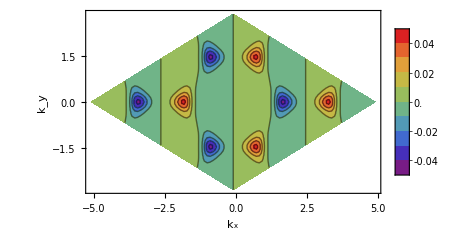
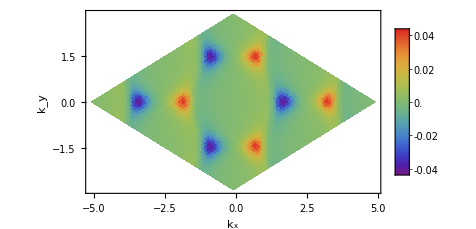
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
{ds2[5],ds2[6],ds2[7]}
```

```mathematica
HAtom=Normal[dsAtom[7]];
HAtom//TraditionalForm
H2=HAtom+M*PauliMatrix[3];
H2//TraditionalForm
```

((1.+0. ⅈ) (-1.27709+0.2398 ⅇ^((0.-2.46882 ⅈ) kx)+0.2398 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000052 ⅇ^((0.-25.6567 ⅈ) ky)+0.000052 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.000061 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.239801 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.239801 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000019 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.000061 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000061 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))) | ⅇ^(ⅈ (0.-1.42537 ky)) (-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000142 ⅇ^((0.-9.87527 ⅈ) kx)-0.000143 ⅇ^((0.+9.87527 ⅈ) kx)+0.000273 ⅇ^((0.-12.3441 ⅈ) kx)+0.000274 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-9.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000079 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))-0.000039 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000113 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000046 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+1.×10^-6 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.00005 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))+2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))+0.000039 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))+0.000039 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.013694 ⅇ^((0.-4.27611 ⅈ) ky)-0.215067 ⅇ^((0.+4.27611 ⅈ) ky)+0.00057 ⅇ^((0.-8.55223 ⅈ) ky)-0.001909 ⅇ^((0.+8.55223 ⅈ) ky)-0.000312 ⅇ^((0.-12.8283 ⅈ) ky)-0.000236 ⅇ^((0.+12.8283 ⅈ) ky)+4.×10^-6 ⅇ^((0.-17.1045 ⅈ) ky)-0.000036 ⅇ^((0.+17.1045 ⅈ) ky)+0.000066 ⅇ^((0.-21.3806 ⅈ) ky)+0.000021 ⅇ^((0.+21.3806 ⅈ) ky)-0.000018 ⅇ^((0.-25.6567 ⅈ) ky)-0.000013 ⅇ^((0.+25.6567 ⅈ) ky)-0.000015 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000027 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000015 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))+0.000077 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000689 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000689 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000016 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-2.82749 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-2.82749 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.009282 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000081 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))+0.0000225 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))-0.000038 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000031 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000211 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000211 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.004839 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.004839 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))+7.×10^-6 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))-0.013694 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))-0.013694 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.00011 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.00011 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))+0.00057 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))+0.00057 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000167 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000027 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.011301 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.011301 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.0000395 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))-0.000039 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))-0.000039 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000057 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))-0.000312 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000689 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000371 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000027 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000027 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-9.×10^-6 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+4.×10^-6 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+0.000057 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))+0.000077 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000143 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000143 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000343 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+0.000066 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-5.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))-0.00002 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))+0.000273 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))+0.000274 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))-0.000081 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000031 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000031 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000039 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000039 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000015 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))-0.000133 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000039 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))-0.000072 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))-0.000072 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000016 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000038 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))+0.000027 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00005 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))+2.×10^-6 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000082 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000046 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.000045 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000036 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000036 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-0.000026 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-0.000026 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-6.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))+0.000015 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))+0.000015 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)))
ⅇ^(ⅈ (1.42537 ky+0.)) (-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000143 ⅇ^((0.-9.87527 ⅈ) kx)-0.000142 ⅇ^((0.+9.87527 ⅈ) kx)+0.000274 ⅇ^((0.-12.3441 ⅈ) kx)+0.000273 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-6.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000043 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+8.×10^-6 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000038 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000016 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))+0.000274 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))+0.000273 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))+0.000182 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000081 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000081 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000016 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000015 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.215067 ⅇ^((0.-4.27611 ⅈ) ky)-0.013694 ⅇ^((0.+4.27611 ⅈ) ky)-0.001909 ⅇ^((0.-8.55223 ⅈ) ky)+0.00057 ⅇ^((0.+8.55223 ⅈ) ky)-0.000236 ⅇ^((0.-12.8283 ⅈ) ky)-0.000312 ⅇ^((0.+12.8283 ⅈ) ky)-0.000036 ⅇ^((0.-17.1045 ⅈ) ky)+4.×10^-6 ⅇ^((0.+17.1045 ⅈ) ky)+0.000021 ⅇ^((0.-21.3806 ⅈ) ky)+0.000066 ⅇ^((0.+21.3806 ⅈ) ky)-0.000013 ⅇ^((0.-25.6567 ⅈ) ky)-0.000018 ⅇ^((0.+25.6567 ⅈ) ky)-0.000036 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000046 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))-0.00005 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000031 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))-0.000343 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-0.004839 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-0.004839 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))-0.001909 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))-0.001909 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))+0.000039 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))+0.000039 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000235 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000043 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+8.×10^-6 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000236 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000236 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))+0.009282 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))+0.009282 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.000072 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.000371 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-6.×10^-6 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.000026 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000031 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000031 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000036 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))-0.000072 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.000142 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.000689 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.002413 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.000015 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000015 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000045 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+2.×10^-6 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))+0.000273 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000077 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))-0.000211 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000039 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000013 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000013 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+8.×10^-6 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000133 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))+0.000027 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))+0.000027 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+1.×10^-6 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-6.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000043 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000039 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000015 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000167 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000167 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000047 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000047 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000082 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000027 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000182 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.000057 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.000057 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000113 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000015 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000038 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00011 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.00002 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.00002 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))-5.×10^-6 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))-0.000039 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))+0.000031 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-9.×10^-6 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000018 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000018 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))) | (1.+0. ⅈ) (-1.27709+0.239801 ⅇ^((0.-2.46882 ⅈ) kx)+0.239801 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000051 ⅇ^((0.-25.6567 ⅈ) ky)+0.000051 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.00006 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.2398 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.2398 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.00006 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.00006 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))))

((1.+0. ⅈ) (-1.27709+0.2398 ⅇ^((0.-2.46882 ⅈ) kx)+0.2398 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.239801 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000052 ⅇ^((0.-25.6567 ⅈ) ky)+0.000052 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.000061 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.000061 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.239801 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.239801 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000019 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000019 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.000061 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.000061 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000061 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000061 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)))+M | ⅇ^(ⅈ (0.-1.42537 ky)) (-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000142 ⅇ^((0.-9.87527 ⅈ) kx)-0.000143 ⅇ^((0.+9.87527 ⅈ) kx)+0.000273 ⅇ^((0.-12.3441 ⅈ) kx)+0.000274 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-9.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000018 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000079 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))+0.000031 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))-0.000039 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000113 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.00002 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.000057 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000047 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000046 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+1.×10^-6 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.00005 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000013 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000039 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.000045 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000031 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.000026 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))+2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.000371 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))+0.009282 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000236 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))+0.000039 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))+0.000039 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))-0.001909 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))-0.000343 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.013694 ⅇ^((0.-4.27611 ⅈ) ky)-0.215067 ⅇ^((0.+4.27611 ⅈ) ky)+0.00057 ⅇ^((0.-8.55223 ⅈ) ky)-0.001909 ⅇ^((0.+8.55223 ⅈ) ky)-0.000312 ⅇ^((0.-12.8283 ⅈ) ky)-0.000236 ⅇ^((0.+12.8283 ⅈ) ky)+4.×10^-6 ⅇ^((0.-17.1045 ⅈ) ky)-0.000036 ⅇ^((0.+17.1045 ⅈ) ky)+0.000066 ⅇ^((0.-21.3806 ⅈ) ky)+0.000021 ⅇ^((0.+21.3806 ⅈ) ky)-0.000018 ⅇ^((0.-25.6567 ⅈ) ky)-0.000013 ⅇ^((0.+25.6567 ⅈ) ky)-0.000015 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000027 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000015 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))+0.000077 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000689 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000689 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000016 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-2.82749 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-2.82749 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.009282 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000081 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))+0.0000225 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))-0.000038 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000031 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000211 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000211 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.004839 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.004839 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))+7.×10^-6 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))-0.013694 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))-0.013694 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))+0.000031 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.00011 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.00011 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))+0.00057 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))+0.00057 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000167 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000027 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.009282 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.011301 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.011301 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.0000395 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))-0.000039 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))-0.000039 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000057 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))-0.000312 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000689 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000371 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000027 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000027 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-9.×10^-6 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+4.×10^-6 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+0.000057 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))+0.000077 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000143 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000143 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000343 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+0.000066 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-5.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))-0.00002 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))+0.000273 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))+0.000274 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))-0.000081 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000031 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000031 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000039 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000039 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000015 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))-0.000133 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000039 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))-0.000072 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))-0.000072 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000016 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000038 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))+0.000027 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00005 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))+2.×10^-6 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000082 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000046 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.000045 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000036 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000036 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-0.000026 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-0.000026 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-6.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))+0.000015 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))+0.000015 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)))
ⅇ^(ⅈ (1.42537 ky+0.)) (-2.82749-0.215067 ⅇ^((0.-2.46882 ⅈ) kx)-0.215067 ⅇ^((0.+2.46882 ⅈ) kx)-0.011301 ⅇ^((0.-4.93763 ⅈ) kx)-0.011301 ⅇ^((0.+4.93763 ⅈ) kx)+0.000371 ⅇ^((0.-7.40645 ⅈ) kx)+0.000371 ⅇ^((0.+7.40645 ⅈ) kx)-0.000143 ⅇ^((0.-9.87527 ⅈ) kx)-0.000142 ⅇ^((0.+9.87527 ⅈ) kx)+0.000274 ⅇ^((0.-12.3441 ⅈ) kx)+0.000273 ⅇ^((0.+12.3441 ⅈ) kx)-0.000133 ⅇ^((0.-14.8129 ⅈ) kx)-0.000133 ⅇ^((0.+14.8129 ⅈ) kx)+0.000039 ⅇ^((0.-17.2817 ⅈ) kx)+0.000039 ⅇ^((0.+17.2817 ⅈ) kx)+0.000082 ⅇ^((0.-19.7505 ⅈ) kx)+0.000082 ⅇ^((0.+19.7505 ⅈ) kx)-0.0000565 ⅇ^((0.-22.2193 ⅈ) kx)-0.0000565 ⅇ^((0.+22.2193 ⅈ) kx)-6.×10^-6 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))+0.000015 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-6.×10^-6 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))+0.000043 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))-0.000026 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))+0.000043 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000036 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+8.×10^-6 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+8.×10^-6 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.000045 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000046 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000082 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))-0.000038 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))+2.×10^-6 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))-0.00005 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))+0.000039 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))-0.000038 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))-0.00011 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000016 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))-0.000072 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))+0.000039 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))-0.000133 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))+0.000031 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))-0.00011 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000039 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000182 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.000031 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))-0.000081 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))-2.×10^-6 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000182 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))+0.000274 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))+0.000273 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))-0.00002 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))-5.×10^-6 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))+0.000066 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000167 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000343 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))+7.×10^-6 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000167 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000143 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))+0.000077 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))+0.000057 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+4.×10^-6 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-5.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-9.×10^-6 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))+0.000027 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))+0.000027 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000371 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))+0.000689 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000211 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))-0.000312 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))+0.000057 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))-0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))-0.000039 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))+0.0000395 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))+0.000182 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))-0.011301 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))+0.009282 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))-0.002413 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000027 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))-0.000167 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))+0.000182 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))+0.00057 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))-0.00011 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-2.×10^-6 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))-0.013694 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))+7.×10^-6 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-2.×10^-6 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.004839 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))-0.002413 ⅇ^(ⅈ (7.40645 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000211 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000031 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))-0.000038 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))+0.0000225 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000081 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000081 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.009282 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))-2.82749 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))-0.004839 ⅇ^(ⅈ (3.70322 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000016 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000689 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))+0.000077 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000015 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))+0.000027 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))-0.000015 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))-0.215067 ⅇ^((0.-4.27611 ⅈ) ky)-0.013694 ⅇ^((0.+4.27611 ⅈ) ky)-0.001909 ⅇ^((0.-8.55223 ⅈ) ky)+0.00057 ⅇ^((0.+8.55223 ⅈ) ky)-0.000236 ⅇ^((0.-12.8283 ⅈ) ky)-0.000312 ⅇ^((0.+12.8283 ⅈ) ky)-0.000036 ⅇ^((0.-17.1045 ⅈ) ky)+4.×10^-6 ⅇ^((0.+17.1045 ⅈ) ky)+0.000021 ⅇ^((0.-21.3806 ⅈ) ky)+0.000066 ⅇ^((0.+21.3806 ⅈ) ky)-0.000013 ⅇ^((0.-25.6567 ⅈ) ky)-0.000018 ⅇ^((0.+25.6567 ⅈ) ky)-0.000036 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))+0.000046 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))-0.00005 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000031 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))-0.000343 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))-0.000343 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000031 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))-0.00005 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))+0.000046 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))-0.000036 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (2.13806 ky-3.70322 kx))-0.004839 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))-0.004839 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))-0.011301 ⅇ^(ⅈ (3.70322 kx+2.13806 ky))-0.001909 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))-0.001909 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))+0.000039 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))+0.000039 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000235 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000043 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+8.×10^-6 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000236 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000236 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+8.×10^-6 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000043 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000235 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (4.27611 ky-7.40645 kx))+0.009282 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))+0.009282 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))-0.000343 ⅇ^(ⅈ (7.40645 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.000072 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.000371 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.000371 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.000072 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))+2.×10^-6 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-6.×10^-6 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))-0.000026 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-6.×10^-6 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000031 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000031 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))-0.000036 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))-0.000072 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))-0.000142 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))+0.000689 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))-0.002413 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))-0.002413 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))+0.000689 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))-0.000142 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))+0.000045 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))+0.000015 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000015 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))+0.000045 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+2.×10^-6 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))+0.000273 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))+0.000077 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))-0.000211 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))-0.000211 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))+0.000077 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))+0.000273 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+2.×10^-6 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))+0.000045 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.000021 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))+0.000039 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))+0.000039 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000013 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000013 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))-0.000026 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))+8.×10^-6 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000081 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))+7.×10^-6 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))+7.×10^-6 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000081 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))+8.×10^-6 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))-0.000026 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))+0.000015 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000133 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))+0.000027 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))+0.000027 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000133 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.00005 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))+1.×10^-6 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))-6.×10^-6 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000043 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-2.×10^-6 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-2.×10^-6 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000043 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))-6.×10^-6 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000039 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000015 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.000167 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.000167 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000015 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000039 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000046 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000047 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000047 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))+0.000082 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000027 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))+0.000182 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.000057 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.000057 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))+0.000182 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000027 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))+0.000082 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))-0.000036 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))-0.000113 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000015 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.000038 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))-0.00011 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.00002 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.00002 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))-0.00011 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.000038 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000015 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))-0.000113 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))-7.5×10^-6 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000045 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))-5.×10^-6 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))-5.×10^-6 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000045 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))-7.5×10^-6 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))-0.000039 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))+0.000031 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))-9.×10^-6 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))-9.×10^-6 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))+0.000079 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-9.×10^-6 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000018 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000018 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-9.×10^-6 ⅇ^(ⅈ (3.70322 kx+23.5186 ky))) | (1.+0. ⅈ) (-1.27709+0.239801 ⅇ^((0.-2.46882 ⅈ) kx)+0.239801 ⅇ^((0.+2.46882 ⅈ) kx)-0.010533 ⅇ^((0.-4.93763 ⅈ) kx)-0.010533 ⅇ^((0.+4.93763 ⅈ) kx)-0.003366 ⅇ^((0.-7.40645 ⅈ) kx)-0.003366 ⅇ^((0.+7.40645 ⅈ) kx)-0.000206 ⅇ^((0.-9.87527 ⅈ) kx)-0.000206 ⅇ^((0.+9.87527 ⅈ) kx)-0.000184 ⅇ^((0.-12.3441 ⅈ) kx)-0.000184 ⅇ^((0.+12.3441 ⅈ) kx)+0.000111 ⅇ^((0.-14.8129 ⅈ) kx)+0.000111 ⅇ^((0.+14.8129 ⅈ) kx)+0.000024 ⅇ^((0.-17.2817 ⅈ) kx)+0.000024 ⅇ^((0.+17.2817 ⅈ) kx)-0.000028 ⅇ^((0.-19.7505 ⅈ) kx)-0.000028 ⅇ^((0.+19.7505 ⅈ) kx)+0.0000115 ⅇ^((0.-22.2193 ⅈ) kx)+0.0000115 ⅇ^((0.+22.2193 ⅈ) kx)-0.00001 ⅇ^(ⅈ (-3.70322 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (-1.23441 kx-23.5186 ky))-0.000017 ⅇ^(ⅈ (1.23441 kx-23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx-23.5186 ky))-0.000038 ⅇ^(ⅈ (-4.93763 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (-2.46882 kx-21.3806 ky))+0.000018 ⅇ^(ⅈ (2.46882 kx-21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (-7.40645 kx-21.3806 ky))-0.000039 ⅇ^(ⅈ (7.40645 kx-21.3806 ky))+0.000056 ⅇ^(ⅈ (-3.70322 kx-19.2425 ky))+0.000056 ⅇ^(ⅈ (3.70322 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (-11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-8.64086 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (-6.17204 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (-1.23441 kx-19.2425 ky))+0.00002 ⅇ^(ⅈ (1.23441 kx-19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx-19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx-19.2425 ky))+0.000031 ⅇ^(ⅈ (-12.3441 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (-9.87527 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (-7.40645 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (-4.93763 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (-2.46882 kx-17.1045 ky))-0.000072 ⅇ^(ⅈ (2.46882 kx-17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx-17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx-17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx-17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx-17.1045 ky))+0.000015 ⅇ^(ⅈ (-13.5785 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (-11.1097 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (-8.64086 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (-6.17204 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (-3.70322 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (-1.23441 kx-14.9664 ky))+0.00005 ⅇ^(ⅈ (1.23441 kx-14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx-14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx-14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx-14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx-14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (-16.0473 kx-14.9664 ky))-0.000038 ⅇ^(ⅈ (16.0473 kx-14.9664 ky))+0.000022 ⅇ^(ⅈ (-12.3441 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (-9.87527 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (-7.40645 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (-2.46882 kx-12.8283 ky))-0.00009 ⅇ^(ⅈ (2.46882 kx-12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx-12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx-12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (-19.7505 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (-17.2817 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (-14.8129 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (-4.93763 kx-12.8283 ky))-0.000084 ⅇ^(ⅈ (4.93763 kx-12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx-12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx-12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx-12.8283 ky))-0.000022 ⅇ^(ⅈ (-11.1097 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (-8.64086 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (-1.23441 kx-10.6903 ky))-0.000174 ⅇ^(ⅈ (1.23441 kx-10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx-10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (-18.5161 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (-16.0473 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (-13.5785 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (-6.17204 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (-3.70322 kx-10.6903 ky))-0.000037 ⅇ^(ⅈ (3.70322 kx-10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx-10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx-10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx-10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (-20.9849 kx-10.6903 ky))-0.000017 ⅇ^(ⅈ (20.9849 kx-10.6903 ky))-0.00009 ⅇ^(ⅈ (-9.87527 kx-8.55223 ky))-0.00009 ⅇ^(ⅈ (9.87527 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (-17.2817 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (-14.8129 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (-12.3441 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (-7.40645 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (-4.93763 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (-2.46882 kx-8.55223 ky))+0.000848 ⅇ^(ⅈ (2.46882 kx-8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx-8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx-8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx-8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx-8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (-22.2193 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (-19.7505 kx-8.55223 ky))+0.000018 ⅇ^(ⅈ (19.7505 kx-8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx-8.55223 ky))-0.000072 ⅇ^(ⅈ (-16.0473 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (-13.5785 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (-11.1097 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (-6.17204 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (-3.70322 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (-1.23441 kx-6.41417 ky))+0.004122 ⅇ^(ⅈ (1.23441 kx-6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx-6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx-6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx-6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx-6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (-8.64086 kx-6.41417 ky))-0.000174 ⅇ^(ⅈ (8.64086 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (-20.9849 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (-18.5161 kx-6.41417 ky))+0.000056 ⅇ^(ⅈ (18.5161 kx-6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx-6.41417 ky))-0.000022 ⅇ^(ⅈ (-14.8129 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (-12.3441 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (-4.93763 kx-4.27611 ky))+0.004122 ⅇ^(ⅈ (4.93763 kx-4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx-4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (-7.40645 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (-2.46882 kx-4.27611 ky))-0.010533 ⅇ^(ⅈ (2.46882 kx-4.27611 ky))+(0.000925-1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (-22.2193 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (-19.7505 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (-17.2817 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (-9.87527 kx-4.27611 ky))-0.000174 ⅇ^(ⅈ (9.87527 kx-4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx-4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx-4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx-4.27611 ky))-0.000084 ⅇ^(ⅈ (-13.5785 kx-2.13806 ky))-0.000084 ⅇ^(ⅈ (13.5785 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (-6.17204 kx-2.13806 ky))+0.004122 ⅇ^(ⅈ (6.17204 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (-3.70322 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (-1.23441 kx-2.13806 ky))+0.2398 ⅇ^(ⅈ (1.23441 kx-2.13806 ky))+(0.041656-1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (-20.9849 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (-18.5161 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (-16.0473 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (-11.1097 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (-8.64086 kx-2.13806 ky))+0.000848 ⅇ^(ⅈ (8.64086 kx-2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx-2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx-2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx-2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx-2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^((0.-4.27611 ⅈ) ky)+(0.041656-1.×10^-6 ⅈ) ⅇ^((0.+4.27611 ⅈ) ky)+(0.000925+1.×10^-6 ⅈ) ⅇ^((0.-8.55223 ⅈ) ky)+(0.000925-1.×10^-6 ⅈ) ⅇ^((0.+8.55223 ⅈ) ky)+0.000133 ⅇ^((0.-12.8283 ⅈ) ky)+0.000133 ⅇ^((0.+12.8283 ⅈ) ky)-0.000035 ⅇ^((0.-17.1045 ⅈ) ky)-0.000035 ⅇ^((0.+17.1045 ⅈ) ky)-8.×10^-6 ⅇ^((0.-21.3806 ⅈ) ky)-8.×10^-6 ⅇ^((0.+21.3806 ⅈ) ky)+0.000051 ⅇ^((0.-25.6567 ⅈ) ky)+0.000051 ⅇ^((0.+25.6567 ⅈ) ky)+0.000031 ⅇ^(ⅈ (2.13806 ky-20.9849 kx))-0.00006 ⅇ^(ⅈ (2.13806 ky-18.5161 kx))+0.000081 ⅇ^(ⅈ (2.13806 ky-16.0473 kx))-0.000037 ⅇ^(ⅈ (2.13806 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (2.13806 ky-8.64086 kx))+0.000848 ⅇ^(ⅈ (8.64086 kx+2.13806 ky))-0.000037 ⅇ^(ⅈ (11.1097 kx+2.13806 ky))+0.000081 ⅇ^(ⅈ (16.0473 kx+2.13806 ky))-0.00006 ⅇ^(ⅈ (18.5161 kx+2.13806 ky))+0.000031 ⅇ^(ⅈ (20.9849 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (2.13806 ky-3.70322 kx))+0.2398 ⅇ^(ⅈ (2.13806 ky-1.23441 kx))+0.2398 ⅇ^(ⅈ (1.23441 kx+2.13806 ky))+(0.041656+1.×10^-6 ⅈ) ⅇ^(ⅈ (3.70322 kx+2.13806 ky))+0.004122 ⅇ^(ⅈ (2.13806 ky-6.17204 kx))+0.004122 ⅇ^(ⅈ (6.17204 kx+2.13806 ky))-0.000084 ⅇ^(ⅈ (2.13806 ky-13.5785 kx))-0.000084 ⅇ^(ⅈ (13.5785 kx+2.13806 ky))-0.0000195 ⅇ^(ⅈ (4.27611 ky-22.2193 kx))+0.000015 ⅇ^(ⅈ (4.27611 ky-19.7505 kx))+0.000022 ⅇ^(ⅈ (4.27611 ky-17.2817 kx))-0.000174 ⅇ^(ⅈ (4.27611 ky-9.87527 kx))-0.000174 ⅇ^(ⅈ (9.87527 kx+4.27611 ky))+0.000022 ⅇ^(ⅈ (17.2817 kx+4.27611 ky))+0.000015 ⅇ^(ⅈ (19.7505 kx+4.27611 ky))-0.0000195 ⅇ^(ⅈ (22.2193 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (4.27611 ky-7.40645 kx))-0.010533 ⅇ^(ⅈ (4.27611 ky-2.46882 kx))-0.010533 ⅇ^(ⅈ (2.46882 kx+4.27611 ky))+(0.000925+1.×10^-6 ⅈ) ⅇ^(ⅈ (7.40645 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (4.27611 ky-14.8129 kx))-0.00009 ⅇ^(ⅈ (4.27611 ky-12.3441 kx))+0.004122 ⅇ^(ⅈ (4.27611 ky-4.93763 kx))+0.004122 ⅇ^(ⅈ (4.93763 kx+4.27611 ky))-0.00009 ⅇ^(ⅈ (12.3441 kx+4.27611 ky))-0.000022 ⅇ^(ⅈ (14.8129 kx+4.27611 ky))-0.000038 ⅇ^(ⅈ (6.41417 ky-20.9849 kx))+0.000056 ⅇ^(ⅈ (6.41417 ky-18.5161 kx))+0.000056 ⅇ^(ⅈ (18.5161 kx+6.41417 ky))-0.000038 ⅇ^(ⅈ (20.9849 kx+6.41417 ky))-0.000174 ⅇ^(ⅈ (6.41417 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (8.64086 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (6.41417 ky-16.0473 kx))+0.00005 ⅇ^(ⅈ (6.41417 ky-13.5785 kx))+0.000133 ⅇ^(ⅈ (6.41417 ky-11.1097 kx))+0.000848 ⅇ^(ⅈ (6.41417 ky-6.17204 kx))-0.003366 ⅇ^(ⅈ (6.41417 ky-3.70322 kx))+0.004122 ⅇ^(ⅈ (6.41417 ky-1.23441 kx))+0.004122 ⅇ^(ⅈ (1.23441 kx+6.41417 ky))-0.003366 ⅇ^(ⅈ (3.70322 kx+6.41417 ky))+0.000848 ⅇ^(ⅈ (6.17204 kx+6.41417 ky))+0.000133 ⅇ^(ⅈ (11.1097 kx+6.41417 ky))+0.00005 ⅇ^(ⅈ (13.5785 kx+6.41417 ky))-0.000072 ⅇ^(ⅈ (16.0473 kx+6.41417 ky))-5.×10^-6 ⅇ^(ⅈ (8.55223 ky-22.2193 kx))+0.000018 ⅇ^(ⅈ (8.55223 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (19.7505 kx+8.55223 ky))-5.×10^-6 ⅇ^(ⅈ (22.2193 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (8.55223 ky-17.2817 kx))-0.000035 ⅇ^(ⅈ (8.55223 ky-14.8129 kx))+0.00005 ⅇ^(ⅈ (8.55223 ky-12.3441 kx))-0.000037 ⅇ^(ⅈ (8.55223 ky-7.40645 kx))-0.000206 ⅇ^(ⅈ (8.55223 ky-4.93763 kx))+0.000848 ⅇ^(ⅈ (8.55223 ky-2.46882 kx))+0.000848 ⅇ^(ⅈ (2.46882 kx+8.55223 ky))-0.000206 ⅇ^(ⅈ (4.93763 kx+8.55223 ky))-0.000037 ⅇ^(ⅈ (7.40645 kx+8.55223 ky))+0.00005 ⅇ^(ⅈ (12.3441 kx+8.55223 ky))-0.000035 ⅇ^(ⅈ (14.8129 kx+8.55223 ky))+0.00002 ⅇ^(ⅈ (17.2817 kx+8.55223 ky))-0.00009 ⅇ^(ⅈ (8.55223 ky-9.87527 kx))-0.00009 ⅇ^(ⅈ (9.87527 kx+8.55223 ky))-0.000017 ⅇ^(ⅈ (10.6903 ky-20.9849 kx))-0.000017 ⅇ^(ⅈ (20.9849 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (10.6903 ky-18.5161 kx))+0.00002 ⅇ^(ⅈ (10.6903 ky-16.0473 kx))-0.000072 ⅇ^(ⅈ (10.6903 ky-13.5785 kx))-0.000184 ⅇ^(ⅈ (10.6903 ky-6.17204 kx))-0.000037 ⅇ^(ⅈ (10.6903 ky-3.70322 kx))-0.000037 ⅇ^(ⅈ (3.70322 kx+10.6903 ky))-0.000184 ⅇ^(ⅈ (6.17204 kx+10.6903 ky))-0.000072 ⅇ^(ⅈ (13.5785 kx+10.6903 ky))+0.00002 ⅇ^(ⅈ (16.0473 kx+10.6903 ky))-8.×10^-6 ⅇ^(ⅈ (18.5161 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (10.6903 ky-11.1097 kx))-0.000084 ⅇ^(ⅈ (10.6903 ky-8.64086 kx))-0.000174 ⅇ^(ⅈ (10.6903 ky-1.23441 kx))-0.000174 ⅇ^(ⅈ (1.23441 kx+10.6903 ky))-0.000084 ⅇ^(ⅈ (8.64086 kx+10.6903 ky))-0.000022 ⅇ^(ⅈ (11.1097 kx+10.6903 ky))-0.000017 ⅇ^(ⅈ (12.8283 ky-19.7505 kx))+0.000018 ⅇ^(ⅈ (12.8283 ky-17.2817 kx))+0.000056 ⅇ^(ⅈ (12.8283 ky-14.8129 kx))-0.000084 ⅇ^(ⅈ (12.8283 ky-4.93763 kx))-0.000084 ⅇ^(ⅈ (4.93763 kx+12.8283 ky))+0.000056 ⅇ^(ⅈ (14.8129 kx+12.8283 ky))+0.000018 ⅇ^(ⅈ (17.2817 kx+12.8283 ky))-0.000017 ⅇ^(ⅈ (19.7505 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.8283 ky-12.3441 kx))+0.000081 ⅇ^(ⅈ (12.8283 ky-9.87527 kx))+0.000111 ⅇ^(ⅈ (12.8283 ky-7.40645 kx))-0.00009 ⅇ^(ⅈ (12.8283 ky-2.46882 kx))-0.00009 ⅇ^(ⅈ (2.46882 kx+12.8283 ky))+0.000111 ⅇ^(ⅈ (7.40645 kx+12.8283 ky))+0.000081 ⅇ^(ⅈ (9.87527 kx+12.8283 ky))+0.000022 ⅇ^(ⅈ (12.3441 kx+12.8283 ky))-0.000038 ⅇ^(ⅈ (14.9664 ky-16.0473 kx))-0.000038 ⅇ^(ⅈ (16.0473 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (14.9664 ky-13.5785 kx))-0.00006 ⅇ^(ⅈ (14.9664 ky-11.1097 kx))+0.000024 ⅇ^(ⅈ (14.9664 ky-8.64086 kx))+0.000081 ⅇ^(ⅈ (14.9664 ky-6.17204 kx))-0.000022 ⅇ^(ⅈ (14.9664 ky-3.70322 kx))+0.00005 ⅇ^(ⅈ (14.9664 ky-1.23441 kx))+0.00005 ⅇ^(ⅈ (1.23441 kx+14.9664 ky))-0.000022 ⅇ^(ⅈ (3.70322 kx+14.9664 ky))+0.000081 ⅇ^(ⅈ (6.17204 kx+14.9664 ky))+0.000024 ⅇ^(ⅈ (8.64086 kx+14.9664 ky))-0.00006 ⅇ^(ⅈ (11.1097 kx+14.9664 ky))+0.000015 ⅇ^(ⅈ (13.5785 kx+14.9664 ky))+0.000031 ⅇ^(ⅈ (17.1045 ky-12.3441 kx))-0.000028 ⅇ^(ⅈ (17.1045 ky-9.87527 kx))-0.00006 ⅇ^(ⅈ (17.1045 ky-7.40645 kx))+0.000022 ⅇ^(ⅈ (17.1045 ky-4.93763 kx))-0.000072 ⅇ^(ⅈ (17.1045 ky-2.46882 kx))-0.000072 ⅇ^(ⅈ (2.46882 kx+17.1045 ky))+0.000022 ⅇ^(ⅈ (4.93763 kx+17.1045 ky))-0.00006 ⅇ^(ⅈ (7.40645 kx+17.1045 ky))-0.000028 ⅇ^(ⅈ (9.87527 kx+17.1045 ky))+0.000031 ⅇ^(ⅈ (12.3441 kx+17.1045 ky))+0.0000115 ⅇ^(ⅈ (19.2425 ky-11.1097 kx))+0.000031 ⅇ^(ⅈ (19.2425 ky-8.64086 kx))+0.000015 ⅇ^(ⅈ (19.2425 ky-6.17204 kx))+0.00002 ⅇ^(ⅈ (19.2425 ky-1.23441 kx))+0.00002 ⅇ^(ⅈ (1.23441 kx+19.2425 ky))+0.000015 ⅇ^(ⅈ (6.17204 kx+19.2425 ky))+0.000031 ⅇ^(ⅈ (8.64086 kx+19.2425 ky))+0.0000115 ⅇ^(ⅈ (11.1097 kx+19.2425 ky))+0.000056 ⅇ^(ⅈ (19.2425 ky-3.70322 kx))+0.000056 ⅇ^(ⅈ (3.70322 kx+19.2425 ky))-0.000039 ⅇ^(ⅈ (21.3806 ky-7.40645 kx))-0.000039 ⅇ^(ⅈ (7.40645 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (21.3806 ky-4.93763 kx))+0.000018 ⅇ^(ⅈ (21.3806 ky-2.46882 kx))+0.000018 ⅇ^(ⅈ (2.46882 kx+21.3806 ky))-0.000038 ⅇ^(ⅈ (4.93763 kx+21.3806 ky))-0.00001 ⅇ^(ⅈ (23.5186 ky-3.70322 kx))-0.000017 ⅇ^(ⅈ (23.5186 ky-1.23441 kx))-0.000017 ⅇ^(ⅈ (1.23441 kx+23.5186 ky))-0.00001 ⅇ^(ⅈ (3.70322 kx+23.5186 ky)))-M)

```mathematica
Clear[h]
h[{kx_,ky_,kz_},M_:2]=H2;
G0={0,0,0};K0={1/3,1/3,0};M0={1/2,0,0};
klabel={"Γ","M","K","Γ"};
ds3=HSPBand[h,lat,{{G0,M0,40},{M0,K0,20},{K0,G0,40}},klabel,efermi]
```

```mathematica
Clear[h]
h[{kx_,ky_,kz_},M_:2]=H2;
bnd=Table[i,{i,1,1}];
ds4=ChernNumberCalc[h,lat,bnd]
```

Dataset[<>]

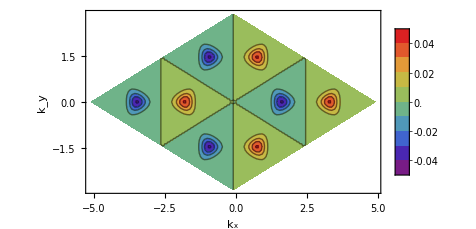
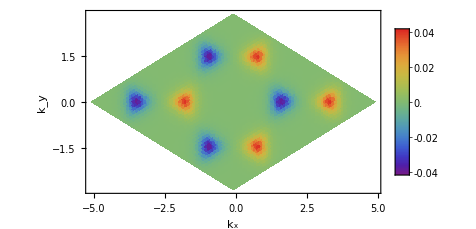
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
{ds4[5],ds4[6],ds4[7]}
```